# Wolfram Science Summer School

## Practice notebook 1

## Introduction

This notebook explains the basic know-how for using the Wolfram Language to do research, starting from scratch. If you are already familiar with this material, skip ahead to the second practice notebook.

If you’re already proficient in other programming languages it might also be worth checking out Fast Introduction for Programmers for a quick introduction to the Notebook interface and more programming-oriented subjects.

## Basic concepts

### Expressions

Everything you find in Mathematica is a Wolfram Language expression. These are like functions, with a function name and arguments, such as

```mathematica
Sin[1.5]
```

With the cursor in the cell above, or with the cell highlighted, one hits ⇧|⌤ to evaluate.

In every expression, there is a Head, followed by a Sequence of arguments wrapped with square brackets. Function arguments can be numbers, symbols, or other Wolfram Language expressions. Built-in functions are capitalized.

In the example above, the Head is Sin and the argument is 1.5. There are many additional built-in functions like List or Table, but everything else is left to the user to define (or not define).

Head, Part and FullForm are built-in functions that help show the structure of an expression, e.g.,

```mathematica
Head[f[x,2,y]]
```

f

Uppercase and lowercase letters are recognized as different characters. Lists are wrapped with curly brackets.
{a, b, B}

To see what argument is at a specific location in an expression, one can use Part.

For instance, to see the third element in a list {g[r],3,s[t],4}

```mathematica
Part[{g[r],3,s[t],4},3]
```

s[t]

Which can be more conveniently written as:

```mathematica
{g[r],3,s[t],4}[[3]]
```

s[t]

Not all expressions are constituted by a head and arguments, for example strings,, numbers and symbols are atomic types. For convenience Head will work with them, but they don’t really have subparts.

Wolfram Language is made of two parts: a kernel and a front end. The kernel is the part that does calculations. The front end is the part that handles notebooks and interaction with the user.

The Mathematica front end sometimes disguises expressions so that they are not explicitly written in the form of a head and arguments enclosed in brackets. For instance it writes 2+z instead of the full Wolfram Language expression Plus[2, z].

Each of these represents multiplication:
a*b a␣b a(b+1) Times[a, b]
2x means 2*x.

The function FullForm is used to display the full Wolfram Language form of an expression:

```mathematica
FullForm[2+z]
```

Plus[2,z]

```mathematica
FullForm[{2,3,s[t],4}]
```

List[2,3,s[t],4]

```mathematica
FullForm[x->1]
```

Rule[x,1]

```mathematica
FullForm[a==b]
```

Equal[a,b]

The following is explained in the Pure Functions section below

```mathematica
FullForm[#+1&]
```

Function[Plus[Slot[1],1]]

Expressions are automatically evaluated, whenever possible, but evaluation can be prevented using Hold. We can use this to see the Expression structure. Note that the following definition of the function g, contained within the braces of Hold, is a Wolfram Language expression.

```mathematica
FullForm[Hold[g[n]:=n^2]]
```

Hold[SetDelayed[g[n],Power[n,2]]]

There is a subtle difference between Set, "=", and SetDelayed, :=, but I won't go into it here, and instead refer you to this exposition in the Help Browser.

There are some exceptions to normal expressions, however only one is sufficiently important to be mentioned now: Association.

Associations are associative arrays (or dictionaries, maps…), they work just like lists, but instead of just indexing elements with position alone, they introduce a key that can be any expression (although in many applications it’s better to just use strings as keys). Associations extend the Part syntax by making it possible to access elements by something different than their position.

```mathematica
assoc = <|"a" -> 1, "b" -> {2,3}|>
```

<|a→1,b→{2,3}|>

Values can be accessed by both key and position:

```mathematica
assoc[[1]]
```

1

```mathematica
assoc[["a"]]
```

1

Part syntax conveniently extends to deeper nested levels:

```mathematica
assoc[["b", 2]]
```

3

#### Question

1. What is the difference between the following two expressions?

```mathematica
x==1
```

```mathematica
x=1
```

The former is comparison (returning a boolean for some defined x, or an equation), the latter is assignment

2. What happens when you evaluate the following expressions in different orders?

To test this properly one might want to use Clear:
Clear[u,v]

```mathematica
Clear[u,v]
```

```mathematica
u=v
```

```mathematica
u:=v
```

```mathematica
v=1
```

```mathematica
v:=0
```

If I immediately assign v = 0,  then immediately or delay assign  u -> v,  they’re both zero
	If I set u = v,  then assign v = 0,   then u is not zero
	If I set u := v, then assign v = 0, then u = 0 at eval time

3. How do you extract the element “this” by using part?

```mathematica
Q3 = {{1,2, {"this"}}}
```

```mathematica
Part[Q3,1,3, 1]
```

this

4. How do you extract the element “this” here?

```mathematica
Q4 = {a, <|"x" -> "this"|>}
```

```mathematica
Q4[[2]][["x"]]
```

this

### Patterns, rules, and function definitions

Suppose you have an expression and you want to change every 1 to a 2 and every 2 to a 1. The easiest way to do this is with a rule application. For instance, here is a Graphics object.

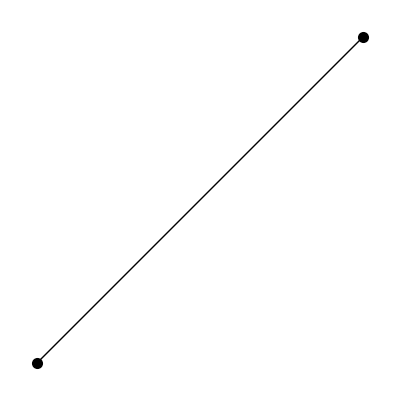

```mathematica
Graphics[{PointSize[.02],Point[{1,4}],Line[{{1,4},{2,5}}],Point[{2,5}]}]
```

Here is the same Graphics object after performing the rule application {1->2, 2->1}, using /., which is short for ReplaceAll. The result is that every occurrence of 1 in the expression becomes 2, and vice versa.

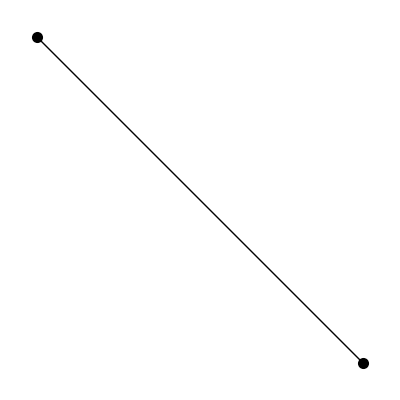

```mathematica
Graphics[{PointSize[.02],Point[{1,4}],Line[{{1,4},{2,5}}],Point[{2,5}]}]/.{1->2,2->1}
```

The left hand side of a rule can be any pattern. By pattern we mean any object or template against which other things will be compared to see if they match. For example, below we use the pattern _Integer which can be roughly translated in English as "any integer". The rule below turns every integer into the variable a.

```mathematica
IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
IdentityMatrix[3]/._Integer->a
```

{{a,a,a},{a,a,a},{a,a,a}}

Temporary variables can be used in a pattern. Here a_Integer means "any integer, temporarily stored in the temporary variable a". The following a has nothing to do with the global variable a.

```mathematica
IdentityMatrix[3]/.a_Integer :> (a+1)^2
```

{{4,1,1},{1,4,1},{1,1,4}}

Note that in the code above I’m not using Rule, but RuleDelayed (:> instead of →). RuleDelayed has the same relationship to Rule as Set has to SetDelayed, and it’s used here to ensure that the a on the right-hand side (rhs) of the rule is the same a as the left-hand side (lhs).

Patterns can be used in other ways like in the functions Count and Cases.

Here we count the number of zeros by using Count on the second level to match the pattern 0. A matrix is a list of lists; the terminology "first level" refers to those lists, while "second level" refers to the elements of those lists. The second level of the identity matrix is composed of 0's and 1's.

```mathematica
Count[IdentityMatrix[3],0,{2}]
```

6

```mathematica
Count[IdentityMatrix[3],1,{2}]
```

3

Here the pattern is any integer.

```mathematica
Count[IdentityMatrix[3],_Integer,{2}]
```

9

On the first level (the default of Count) of a matrix, there are only lists, no integers.

```mathematica
Count[IdentityMatrix[3],_Integer]
```

0

A pattern can just consist of the single _ or Blank[] which represents any single expression.

```mathematica
Count[IdentityMatrix[3],_]
```

3

```mathematica
Count[{g[r],2,s[t],4,s[5],S[3]},s[_]]
```

2

Below, Cases is used to find every case of a subexpression with the Head "s".

```mathematica
Cases[{g[r],2,s[t],4,s[5],S[3]},_s]
```

{s[t],s[5]}

You will also see patterns appear in another part of the language, namely function definition. In order to define a function that takes any single argument one would write:

```mathematica
f[x_] := x^2
```

You can use pattern matching to prevent functions from evaluating when the arguments don’t match a certain type:

```mathematica
factor[x_Integer] := FactorInteger[x]
```

Now factor will only evaluate when its argument is an integer:

```mathematica
factor["string"]
```

factor[string]

```mathematica
factor[4]
```

{{2,2}}

Pattern matching in function definitions is also very useful when one declares multiple definitions for the same function. This concept is usually called polymorphism and can be used to write very concise and expressive code. However it seems a bit early to go into depth. We will cover this concept later.

#### Questions

1. Unintended consequences are common in programming. What is going on in the following alteration of the previous Graphics example? Why are the colors different?

```mathematica
Graphics[{Hue[.99],PointSize[.2],Point[{1,4}],Hue[.3],Line[{{1,4},{2,5}}],Hue[.95],Point[{2,5}]},PlotRange->{{-1,3},{3,6}}]/.{1->.3,2->1.5}
```

```mathematica
Graphics[{Hue[1],PointSize[.2],Point[{1,4}],Hue[.3],Line[{{1,4},{2,5}}],Hue[.95],Point[{2,5}]},PlotRange->{{-1,3},{3,6}}]/.{1->.3,2->1.5}
```

In the first example,  1 -> .3 does not affect the Hue of the first node, but changes node positions.
	In the second example, 1 -> .3 also (unintentionally?) modifies the coincidentally-unity Hue of the first node.

2. In the following example, change every Point to a Circle with radius 1/2, centered around the point, using a Rule application.

(Try using Help to see how to use Circle, and remember to use a Rule application instead of re-typing the whole expression).

```mathematica
Graphics[{PointSize[.02],Point[{9,5}],Point[{2,-5}],Point[{5,5}],Point[{3,6}],Point[{1,1}],Point[{5,-7}],Point[{-7,4}],Point[{6,-10}],Point[{-6,-2}],Point[{0,8}],Point[{1,4}],Line[{{1,4},{2,5}}],Point[{2,5}]},AspectRatio->Automatic] /. Point[{a_Integer, b_Integer}] :> Circle[{a,b},{1/2,1/2}]
```

3. Another unintended consequence of ReplaceAll is that sometimes you don’t really want to replace all of the occurrences of a symbol, for example the following code has the effect of modifying the argument of s as well as the values in the list:

```mathematica
{1,2, s[1]}/. 1-> "one"
```

{one,2,s[one]}

How would you modify the code above by using the function Replace so that s[1] is left untouched (hint: second usage description in the documentation of Replace).

```mathematica
Replace[ {1,2, s[1]}, 1 -> "one", {1}]
```

{one,2,s[1]}

4. Write a function that doubles integers and doesn’t evaluate on even numbers

### Pure functions

The Wolfram Language supports many programming styles, but one of the most natural is the functional paradigm. One of the key features of functional programming is that one can define anonymous functions or lambdas and treat them as any other value in the language: they can be assigned to variables and passed as function arguments. Wolfram Language programmers often call anonymous functions pure, though in other programming languages pure has a slightly different meaning.

```mathematica
square=#^2&
```

#1^2&

```mathematica
sq[x_] := x^2
```

By default # represents the first argument of a function, and can alternatively be written as #1.

```mathematica
FullForm[square]
```

Function[Power[Slot[1],2]]

Note the importance of the &, which is needed to make it a function:

```mathematica
FullForm[#^2]
```

Power[Slot[1],2]

Pure functions can be applied like any other function.

```mathematica
square[3]
```

9

```mathematica
sq[3]
```

9

A pure function can take any number of arguments.

```mathematica
square[3,4]
```

9

```mathematica
sq[3,4]
```

sq[3,4]

```mathematica
superpower=#1^(#2^#3)&
```

#1^(#2^#3)&

```mathematica
FullForm[superpower]
```

Function[Power[Slot[1],Power[Slot[2],Slot[3]]]]

```mathematica
superpower[2,3,4]
```

2417851639229258349412352

```mathematica
3^4
```

81

```mathematica
2^%
```

2417851639229258349412352

The % symbol is used to represent the most recent output.

Note that a pure function does not need to be set as a symbol, e.g.,

```mathematica
#+#2^#3&[2,3,4]
```

83

Pure functions have been extended to be more convenient to use with associations, for example:

```mathematica
#x^2&[<|"x" -> 4|>]
```

16

```mathematica
FullForm[#x]
```

Slot["x"]

Be careful though, this syntax only works with string keys not containing spaces or starting with numbers.

### Using functions with Lists and Associations

There are several situations where one wants to use a function on every element in a list.

Suppose you have a list, and you want to apply a function to every element in that list separately. The right way to do this is to use the function Map.

```mathematica
Map[f,{a,b,c,d}]
```

```mathematica
{f[a],f[b],f[c],f[d]}
```

The same applies to an Association, however the function is only applied to the values

```mathematica
Map[f, <|"a" -> a, "b" -> b|>]
```

<|a→f[a],b→f[b]|>

It’s generally useful to remember that functions that operate on lists will operate only on the values of an association unless otherwise specified. Exceptions usually have Key in their name (KeyValueMap, KeySort, etc…).

Other important operations on Association are Normal, which turns it into a list of rules, Keys, and Values.

Say we have a random matrix of 0's and 1's, and we want to take the Total of each row.

```mathematica
randombits=RandomInteger[{0,1},{5,5}]
```

{{0,0,1,0,0},{1,1,1,0,1},{0,0,0,1,0},{1,1,1,1,1},{1,1,1,1,0}}

```mathematica
randombits//MatrixForm
```

(0 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0)

Use Map, or equivalently the short cut /@, with Total as follows:

```mathematica
Total/@randombits
```

{1,4,1,5,4}

Now let's take a matrix of digits, and say we want to know which digits occur. The function to use is Union.

```mathematica
randomdigits=RandomInteger[{0,9},{3,3}]
```

{{6,5,2},{4,5,5},{9,3,4}}

```mathematica
randomdigits//MatrixForm
```

(6 | 5 | 2
4 | 5 | 5
9 | 3 | 4)

However, if we try Union, it doesn't do what we wanted because we asked it to take a union of a list of three lists. The three lists are considered basic units.

```mathematica
Union[randomdigits]
```

{{4,5,5},{6,5,2},{9,3,4}}

Instead, we want to take a union of the three lists. One approach is to use the function Apply. It replaces the head of the expression with Union.

```mathematica
Apply[Union, randomdigits]
```

{0,1,2,3,4,5,6,7,9}

```mathematica
Apply[f, randomdigits]
```

f[{0,1,3},{2,4,9},{6,5,7}]

As with Map, the function Apply also has a shortcut, @@

```mathematica
Union@@randomdigits
```

{0,1,2,3,4,5,6,7,9}

To better understand what Apply does, use a function that has no definition:

```mathematica
Apply[q,{1,2,3}]
```

q[1,2,3]

```mathematica
Apply[q, r[1,2,3]]
```

q[1,2,3]

As you can see all Apply is doing is replacing the head with another head. For more visualizations of basic functions you can visit this page.

#### Questions

1. Use Map and Count to find the number of 1's on each row of the following matrix.

Hint: you might want to use a pure function with Count.

```mathematica
m = RandomInteger[1, {10, 10}]
```

{{0,1,1,0,1,1,0,1,1,0},{0,0,1,0,0,0,0,0,1,0},{1,1,0,1,0,0,0,1,0,1},{0,1,1,1,1,1,1,0,0,0},{1,0,0,0,1,0,1,1,1,0},{1,1,0,1,1,0,0,0,0,0},{1,0,1,1,0,0,0,0,1,0},{1,1,0,0,0,1,0,0,0,0},{0,1,1,0,1,1,1,1,1,0},{0,0,1,0,0,0,1,1,0,0}}

```mathematica
Map[Count[#1, 1, {1}] &, m]
```

{6,2,5,6,5,4,4,3,7,3}

2. Use Apply and SameQ to determine if all of the arguments of the expression below are the same. Why might they be the same even though they appear different?

```mathematica
f[c,d,a,b]
```

```mathematica
Apply[SameQ, f[c,d,a,b]]
```

Not sure what this question is asking. SameQ compares expression trees. c, d, a and b are just symbols. They could have the same substituted values (mathematically), but SameQ would only return true for f[a, a, a, a]

3. Using the Level specification, use Apply and Max to find the maximum value of each row of the following matrix:

```mathematica
mm = RandomReal[10, {10, 10}];
```

```mathematica
Apply[Max, mm, {1}]
```

4. Given the following association, return an association where the keys are unchanged and the values are the mean of each list:

```mathematica
assoclist = <|"first" -> {1,Pi,3.}, "second" -> {2., 20}|>;
```

```mathematica
Map[Mean, assoclist, {1}]
```

5. Given the association above, return an association where each key is unchanged and each value is the StringLength of the corresponding key.

```mathematica
AssociationMap[ StringLength[#1]&, Keys[assoclist]]
```

<|first→5,second→6|>

### Basic vocabulary of functions

There are many basic functions everyone should know.  We have seen here some of the most commonly used:  Equal, Part, List, SetDelayed, ReplaceAll, Pattern, Blank, Rule, Slot, Function. Note that each of these functions has a short form representation. Recall =, {}, :=, /., _, #, &, etc.

After learning those, another collection of important functions are Table, Array, Map, Apply, Fold, and other similar functions.

#### Questions

1. Write a short piece of code which sums the first n primes, using the built-in functions Array, Fold, Plus and Prime.

```mathematica
n = 20;
```

```mathematica
Fold[Plus, 0, Array[Prime, n]]
```

2. Make the same function using the built-in functions Apply, Plus, Prime and Table.

```mathematica
Fold[Plus, 0, Table[Prime[i], {i, n}]]
```

3. Do it again, using just Prime and Sum.

```mathematica
Sum[ Prime[i], {i, n}]
```

### Advanced function definition, pattern matching and recursion

A very common idiom in the Wolfram Language is to have multiple definitions for the same function. This is called polymorphism and it’s a very expressive way of normalizing arguments or defining recursive functions.

```mathematica
symbolLength[s_Symbol] := symbolLength[SymbolName[s]]
symbolLength[s_String] := StringLength[s]
symbolLength[_] := $Failed
```

```mathematica
symbolLength[List]
```

4

The function above takes either a string or a symbol, and computes the character length of either. It’s easy to understand that when the function is called with a symbol it will first turn it into a string using SymbolName; the problem is then reduced to the one of finding the length of a string. One could just as well define symbolLength as:

```mathematica
symbolLength2[s_] := If[
MatchQ[s, _Symbol],
StringLength[SymbolName[s]],
If[
StringQ[s],
StringLength[s],
$Failed
]
]
```

But this is a lot less concise and one kind of loses sight of the mathematics of the problem.

Another classical example of recursion is the definition of the factorial:

```mathematica
fact[0] := 1
fact[n_] := n fact[n-1]
```

```mathematica
fact[6]
```

720

But what is the theory behind all this? How can I know what function definition is going to be applied first? How do I know if a function definition overwrites another? DownValues is a good place to start:

```mathematica
DownValues[fact]
```

{HoldPattern[fact[0]]:>1,HoldPattern[fact[n_]]:>n fact[n-1]}

DownValues returns all definitions as a list of rules in the order they are tried. There are a couple of things that one needs to pay attention to when writing multiple function definitions:

1. Identical left hand sides overwrite one another:

```mathematica
g[2] := 1
g[2] := 2
DownValues[g]
```

{HoldPattern[g[2]]:>2}

Sometimes two definitions are effectively the same, but not exactly the same:

```mathematica
h[x_] /; x== 2. :=1
h[x_] /; x== 2 := 2
DownValues[h]
```

{HoldPattern[h[x_]/;x==2.]:>1,HoldPattern[h[x_]/;x==2]:>2}

Here we’ve introduced a new concept /; also known as Condition, which is an expression to be evaluated before evaluating the body of the function. The body of the function is evaluated only if the condition has evaluated to True.

In this case the DownValue doesn’t get overwritten, and definitions get tried in order. So without trying, what is h[2]? Why?

2

```mathematica
h[2]
```

1

I see. So polymorphism allows multiple equivalent definitions with different expression trees, and whichever appears first in DownValues is called.

2. In some very obvious cases DownValues can get reordered from the least general to the most general:

```mathematica
i[x_] := x
i[1] := "one"
DownValues[i]
```

{HoldPattern[i[1]]:>one,HoldPattern[i[x_]]:>x}

Deciding whether one pattern is more or less general than another is generally undecidable, so you should not rely on this behavior too much. Rather put your definitions in the order you expect them to be tried.

3. Condition (/;) and PatternTest (?) are very useful when defining complex patterns:

```mathematica
oddDouble[x_?OddQ] := 2x
oddDouble[x_] := x
oddDouble /@ Range[5]
```

{2,2,6,4,10}

4. DownValues can be added when executing the function itself, this technique can be used to memorize a function. Let’s consider our factorial example:

```mathematica
fact2[n_] := fact2[n] = n fact2[n-1]
fact2[0] := 1
```

```mathematica
fact2[5]
```

120

```mathematica
DownValues[fact2]
```

{HoldPattern[fact2[0]]:>1,HoldPattern[fact2[1]]:>1,HoldPattern[fact2[2]]:>2,HoldPattern[fact2[3]]:>6,HoldPattern[fact2[4]]:>24,HoldPattern[fact2[5]]:>120,HoldPattern[fact2[n_]]:>(fact2[n]=n fact2[n-1])}

As you can see by dynamically adding new cases to the DownValues you can skip the whole computation.

#### Questions

1. Define a function that can takes three real numbers between 0 and 1 and returns the RGBColor corresponding to it. Now make it work on lists of triples.

```mathematica
f[a_, b_, c_] /; 0<a<1 && 0<b<1 && 0<c<1= RGBColor[a, b, c]
```

Going to allow unpacking tuple if numbers are outside (0, 1).

```mathematica
f[{a_, b_, c_}] = f[a, b, c]
```

2. Using recursion define a function that returns the nth Fibonacci number. Why is it so slow to compute the 100th Fibonacci number? How can you speed it up?

Here’s a shitty O(2^N) (double recursive call) version

```mathematica
fib[1] = 1;
fib[2] = 1;
fib[n_Integer] := fib[n-1] + fib[n-2];
```

Here’s an O(N) version (same definition) using dynamic programming

```mathematica
fib2[1] = 1;
fib2[2] = 1;
fib2[n_Integer] := fib2[n] = fib2[n-1] + fib2[n-2];
```

Here’s an O(N) non-dynamic tail-recursion (or at least, single recursive call) version

```mathematica
fib3[1, p1_Integer, p2_Integer] = p1;
fib3[n_Integer, p1_Integer, p2_Integer] :=fib3[n-1, p1+p2,p1];
fib3[n_Integer] := fib3[n, 1, 0];
```

3. Write a function that takes the following string:

```mathematica
"<b>Hello</b> <i>stranger</i>"
```

and returns:

```mathematica
Row[{Style["Hello", Bold], " ", Style["stranger", Italic]}]
```

Hello stranger

(hint: use string patterns and recursion)

```mathematica
str = "<b>Hello</b> <i>stranger</i>, how are <b><i>you</i></b>?";
```

I’m too tired to handle nested bolds (trying to capture both adjacent and nested bolds is hard in regex); I’m just going to assume there’s no nesting of bolds (and italics).

```mathematica
boldmatch = RegularExpression["<b>(.+?)</b>"];
```

```mathematica
italicsmatch =  RegularExpression["<i>(.+?)</i>"];
```

Base case (no bolds or italics left) returns the string

```mathematica
decomp[stri_] /;  (!StringContainsQ[stri, boldmatch]) && (!StringContainsQ[stri, italicsmatch ])  :=  stri
```

replace bolds with decomp on them (the second decomp will match italics)

```mathematica
decomp[stri_] /; StringContainsQ[stri, boldmatch] ||  StringContainsQ[stri, italicsmatch]:= Row[StringSplit[stri, {boldmatch -> Style[decomp["$1"], Bold],  italicsmatch -> Style[decomp["$1"], Italic]}]]
```

```mathematica
decomp["<b> finally </b> my noisy neighbour <b> has quitened </b> <i> <b> down </b> </i> "]
```

finally  my noisy neighbour  has quitened   <b> down </b>

This doesn’t handle <b> <i> etc </i> </b> because a string is split into a row containing (non-matching substrings) and (expressions of matching substrings), and the matching substring expressions are populated with (recursively fetched) rows. Recursing N times yields N-deep rows, for which style doesn’t seem to handle (though I’m very tired...))

I think I could fix this by only calling row only once (with an overload), and overloading decomp to handle list packing and unpacking when recursing